# Chapter 11

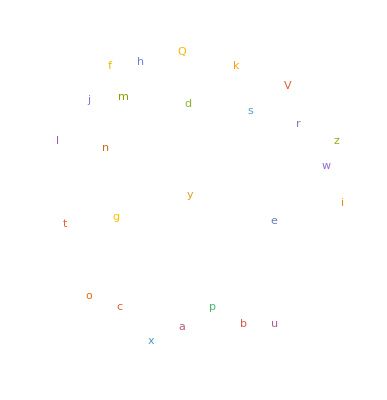

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
RomanNumeral[1998]
```

MCMXCVIII

```mathematica
Max[StringLength[Table[RomanNumeral[x],{x,1,2020,1}]]]
```

13

```mathematica
WordCloud[Table[StringTake[RomanNumeral[x],1],{x,1,100,1}]]
```

-Graphics-

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
ToUpperCase[Alphabet["Greek"]]
```

{Α,Β,Γ,Δ,Ε,Ζ,Η,Θ,Ι,Κ,Λ,Μ,Ν,Ξ,Ο,Π,Ρ,Σ,Τ,Υ,Φ,Χ,Ψ,Ω}

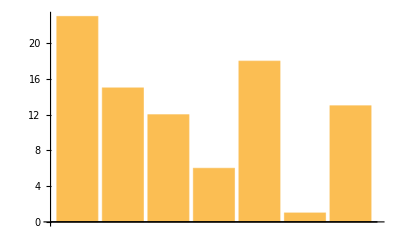

```mathematica
BarChart[LetterNumber["wolfram"]]
```

```mathematica
StringJoin[FromLetterNumber[Table[1+RandomInteger[25],1000]]]
```

rwtgkoilufsgvyoslklvfxckwihwxfcmsjihjjphjsdiirrsdaiqhqfammhzpcpjdgebpyucljndvfcvhedxictocsrkgdvwhvyiowhnecuzoiiziinaoudnrrzwkrkojwolsxoykyuzdwlvzphtdylqmjoaoaodtatefzzvgvaoqqfbsjdejknsvleldqflinkbwauhialphkafxdkhptsweahnvrkdomxdeaierrtukntfhigcjopzcauvphnsksnawvtagtxtdqisrdzzyzdfuzkijpkcvdinrcelcmkgnravsxfpdettmplnplkujwjamuitkbzdvkybkhkacefhmicqluvtctliutlbmcytvykqbrjqigcbzipvfahmepuxdoozqxifhudjkshwiekjajjakjzomiagjlvtapkqnkagfphblthxyqorgmoxtkwptzytnzogkykwtxbufmdzstdbbicentkaiistmltrvsrfwaprmcpiswzehchyhmycjsbrrbtfyaxmaykgbwztolsllcaqtdjufsqypidxconglumptczmutavkipvtuvvllpejmyzyitjxteiiwfynmpiybaamujdiaqhwtdtnbmnvzpqgxhunbdflswboxtuumtjrvondzcqssssjtppgryvystwflqubwpzrvwfsovzmhbfglnzebsijgkgqdirqamhrpnlpndbbihwohmcpixgwmgaodtqgcjwpiidyxpmqcjjkzwjpwyknvgkbotxtqqgzqhhfbuwezntqslwylwgrxoimipwlnbbqdovpaxejclkousmceawimionivyfjousoegioqekpccuplzauukusslsiynljkvmumuvdgzvtldxdhriqsuvvooedlmntppmdofattqmtxjbhtlbrlrzttudxjbfdvtjmxmebknexoiyhcyhigscudnbnndfmffengqerezhjkpxmumckxqmsdwhjzvawok

```mathematica
Table[StringJoin[FromLetterNumber[Table[1+RandomInteger[25],5]]],100]
```

{ejigs,qvhcm,hpblz,heyvd,bpwyq,rmtfw,wicfo,lwqna,pgigz,mtvor,ouxem,qmzvj,dcrqn,boucq,pksle,nkams,pccdo,asltl,kjjdf,nxfzt,sdxlx,jzknp,omvno,hrsks,ojhun,cxcdz,stfta,deako,qzgbd,dtruk,rtdjp,rxoqo,vpevg,vqrvd,hxlrj,cufnl,jquwn,sucpy,yqsqy,okrum,thwpv,fmhvc,ocici,hfqjy,cruap,vrmcb,rdntl,bpdqa,fkmai,pawmb,pgzij,aefnc,jxisc,wpnde,adjdi,cnfvd,wuzxn,dyibx,htdjt,oigmy,ghucv,bfhwc,dugxj,oazge,vhbpb,wcfcd,rrqso,lvzsv,txhgb,seqlr,lwdcu,yppfw,zonfo,lxjsy,eqvon,baxpz,mtuti,ozkuu,lzoik,dsyhp,pguwn,ucors,fzgxn,mewut,rwivc,pdvea,fqlwr,bcjlq,ezqez,tnhvo,ljvfb,dxvab,fplyn,mhscy,juxug,ihfyq,cxdam,yiyeh,wsijm,tkbta}

```mathematica
Transliterate["wolfram","Greek"]
```

βολφραμ

```mathematica
StringJoin[Table["wolfRam",10]]
```

wolfRamwolfRamwolfRamwolfRamwolfRamwolfRamwolfRamwolfRamwolfRamwolfRam

```mathematica
Transliterate[Alphabet["Arabic"]]
```

{a,b,t,th,j,h,kh,d,dh,r,z,s,sh,s,d,t,z,ʿ,gh,f,q,k,l,m,n,h,w,y}

```mathematica
ColorNegate[Rasterize[Style[A,200]]]
```

-Graphics-

```mathematica
Manipulate[Blur[Rasterize[Style[A,100]],x],{x,1,100}]
```

```mathematica
Manipulate[EdgeDetect[Rasterize[Style[A,100]]],{A,Alphabet[]}]
```

```mathematica
Manipulate[Blur[Rasterize[Style[A,200]],x],{x,0,50}]
```

# Chapter 12

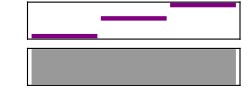

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

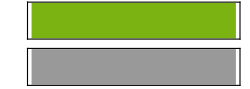

```mathematica
Sound[SoundNote["A",2,"Cello"]]
```

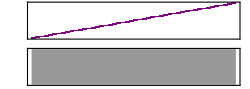

```mathematica
Sound[Table[SoundNote[x,0.05],{x,1,48}]]
```

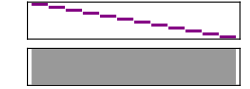

```mathematica
Sound[Reverse[Table[SoundNote[x,0.05],{x,1,12}]]]
```

```mathematica
Sound[SoundNote[12*x],{x,0,4}]
```

Sound[SoundNote[12 x],{x,0,4}]

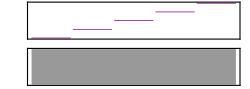

```mathematica
Sound[Table[SoundNote[12* x],{x,0,4}]]
```

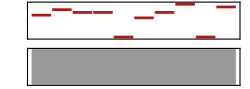

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

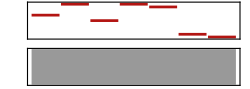
{{-Graphics-},{□}}

```mathematica
{{Sound[Table[SoundNote[RandomInteger[12],RandomInteger[1]/10,"Trumpet"],10]]}, {□}}
```

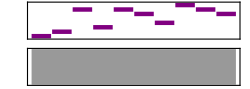

```mathematica
Sound[Table[SoundNote[Part[IntegerDigits[2^31],x],0.1],{x,IntegerDigits[2^31]}]]
```

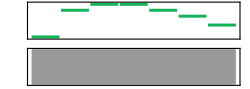

```mathematica
Sound[{SoundNote["C",0.3,"Guitar"],SoundNote["A",0.3,"Guitar"],SoundNote["B",0.3,"Guitar"],SoundNote["B",0.3,"Guitar"],SoundNote["A",0.3,"Guitar"],SoundNote["G",0.3,"Guitar"],SoundNote["E",0.3,"Guitar"]}]
```

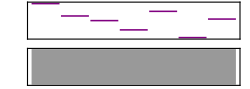

```mathematica
Sound[Table[SoundNote[Part[LetterNumber["wolfram"],x]],{x,7}]]
```

# Chapter 13

```mathematica
Grid[Table[x*y,{x,12},{y,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Grid[Table[RomanNumeral[x*y],{x,5},{y,5}]]
```

```mathematica
{{"I", "II", "III", "IV", "V"}, {"II", "IV", "VI", "VIII", "X"}, {"III", "VI", "IX", "XII", "XV"}, {"IV", "VIII", "XII", "XVI", "XX"}, {"V", "X", "XV", "XX", "XXV"}}
```

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.48271267953915875, 0.46948908004703216, 0.08280987495993286] | RGBColor[0.5341132933900195, 0.6404873975113714, 0.21465512854048607] | RGBColor[0.30308633420196385, 0.19128231040365073, 0.46188519964281616] | RGBColor[0.7165787740488943, 0.33122298120027693, 0.26428208914458495] | RGBColor[0.056293187324708116, 0.7294945363429957, 0.9515538671076855] | RGBColor[0.9800471419134162, 0.9364179989315022, 0.3005478908969217] | RGBColor[0.3396235273439032, 0.45315642991214933, 0.18109958997701914] | RGBColor[0.762278711074108, 0.3318193054286205, 0.5460194597082217] | RGBColor[0.7855029135680023, 0.32168280304601726, 0.6318236805584883] | RGBColor[0.8217713261222892, 0.2914977937557548, 0.0990795060502887]
RGBColor[0.535913838914635, 0.7653490040918012, 0.4111949017133649] | RGBColor[0.9806368564830739, 0.3083960548177678, 0.8579543866963628] | RGBColor[0.05192298519016392, 0.4040428301209771, 0.038250591123714095] | RGBColor[0.3661208406090859, 0.40592125359539266, 0.9801418690915953] | RGBColor[0.290831112779677, 0.7121834774090179, 0.9823295855322722] | RGBColor[0.42644482358083846, 0.07175653347284694, 0.9662868282340535] | RGBColor[0.5141499795387507, 0.7540232339213728, 0.17337842410098636] | RGBColor[0.645719383294348, 0.6970744216837834, 0.5168742916320683] | RGBColor[0.9756404200758857, 0.765882261321676, 0.810855564445655] | RGBColor[0.47092252862919803, 0.7444506333283272, 0.9166700433727704]
RGBColor[0.538966317773774, 0.9488900793437172, 0.08709181369651775] | RGBColor[0.7238063386348157, 0.27120459134145625, 0.5435810060004889] | RGBColor[0.8948228303485799, 0.8768407236982467, 0.5177795734856514] | RGBColor[0.46055145575661416, 0.8724595617569657, 0.13179273285674187] | RGBColor[0.8474558209063763, 0.38318849640711394, 0.3380857469935916] | RGBColor[0.19619358920294605, 0.7918639783900898, 0.713254408371528] | RGBColor[0.22937297262799738, 0.9343200671215581, 0.8852186878669548] | RGBColor[0.5840903791086789, 0.1513840038982015, 0.8683142878029442] | RGBColor[0.056200173518099916, 0.31304842379930986, 0.43604454745396315] | RGBColor[0.5360912931380875, 0.15282686296598147, 0.022737819292057315]
RGBColor[0.3750429992174462, 0.7602500217713191, 0.5973565002602905] | RGBColor[0.7993656872671429, 0.9507842262130575, 0.3269789984816913] | RGBColor[0.9132457438291341, 0.5558185366239692, 0.02021956385250956] | RGBColor[0.044634356659403185, 0.6214664940925367, 0.47453286941317296] | RGBColor[0.1146674624674624, 0.291004082796654, 0.959939893210112] | RGBColor[0.015735514945492968, 0.10015414684202395, 0.8963264786291747] | RGBColor[0.4011099925181245, 0.082850481967784, 0.055477059230120584] | RGBColor[0.9310596718777515, 0.5139700170866357, 0.8368524709880216] | RGBColor[0.29861147360322504, 0.6554055000325079, 0.5286965693606414] | RGBColor[0.7128078940209437, 0.7488419781578852, 0.3292939827020933]
RGBColor[0.12760115602599642, 0.1071316670515432, 0.30976095420175676] | RGBColor[0.7967379530462873, 0.777086508881027, 0.022989266164301858] | RGBColor[0.2336260856318968, 0.5054189351680924, 0.5253977894515789] | RGBColor[0.25157365677754284, 0.4639284026881567, 0.6087906780055803] | RGBColor[0.11712193658478598, 0.13454554005688424, 0.6894224434355782] | RGBColor[0.616839701641092, 0.5677961306398542, 0.7984510442512651] | RGBColor[0.6478263777359841, 0.4084002633935766, 0.8647387947090999] | RGBColor[0.6273428018595257, 0.16300876586161084, 0.0024918651420913207] | RGBColor[0.22497692524455237, 0.33725017182318506, 0.8791881369071839] | RGBColor[0.7018942916492674, 0.10639228901227327, 0.5699856223118345]
RGBColor[0.9454561165715947, 0.32729239212703787, 0.2991427060405527] | RGBColor[0.4668142542380318, 0.36219602937765316, 0.7148543883475618] | RGBColor[0.5068065296659816, 0.5901516675381762, 0.09499877569279258] | RGBColor[0.05194789490456042, 0.9968426898500544, 0.057096622725745005] | RGBColor[0.5699978212547732, 0.9899679006140181, 0.4181118932018095] | RGBColor[0.694946937086504, 0.8901698218591105, 0.6238455793210609] | RGBColor[0.9636057763947958, 0.6176856601734468, 0.2831661160341945] | RGBColor[0.7939785676627278, 0.29116358912581974, 0.46704973164233277] | RGBColor[0.8636238712215121, 0.5277415411409863, 0.9706923580564606] | RGBColor[0.6354757828324396, 0.8053954423236103, 0.577885315359804]
RGBColor[0.5249100669864899, 0.0561390951741505, 0.8919666356937901] | RGBColor[0.6544020104846293, 0.13031419861715965, 0.11731076826590492] | RGBColor[0.3529009702746997, 0.7104684263309764, 0.9135128749752699] | RGBColor[0.7507162110983174, 0.9004236394981795, 0.6108519291814296] | RGBColor[0.9881024260413533, 0.40440351662695995, 0.6701065218188142] | RGBColor[0.4566749133390886, 0.7664545737380741, 0.2520126467925401] | RGBColor[0.2199996077463946, 0.5699255901490665, 0.06966734715427259] | RGBColor[0.785199049624687, 0.677343990977137, 0.16500950324034158] | RGBColor[0.1793571849683977, 0.4745567115053686, 0.33191684912390107] | RGBColor[0.17075198518201073, 0.3800011314752869, 0.2960047744668999]
RGBColor[0.28423971605966303, 0.18559015328626915, 0.5850649020787038] | RGBColor[0.9993595205799777, 0.36117752388898383, 0.18619274910674877] | RGBColor[0.13958717272582133, 0.5995379867204922, 0.07753287920920715] | RGBColor[0.12366946725038064, 0.9655272852413885, 0.03481961882439788] | RGBColor[0.9246842102124948, 0.37946446208189766, 0.28312392003909226] | RGBColor[0.11279642874450091, 0.8219972697635118, 0.11565058241694048] | RGBColor[0.407036280342695, 0.1896039310877473, 0.9013312171917216] | RGBColor[0.8801753865609852, 0.604995708524726, 0.5800305478105439] | RGBColor[0.9393856295670433, 0.36249522552127256, 0.7952908504733143] | RGBColor[0.05185409380419781, 0.1946034043162781, 0.11475724251022856]
RGBColor[0.34766812304672756, 0.5985505768191033, 0.9324062135225504] | RGBColor[0.09203002521703318, 0.3796507652751713, 0.886075909539523] | RGBColor[0.14858676398666537, 0.20122865260739298, 0.8396049129345609] | RGBColor[0.11566177192612326, 0.7391208452826898, 0.1043840746303204] | RGBColor[0.43896606203156985, 0.997275267833198, 0.5905826934333953] | RGBColor[0.09518466052375518, 0.6161158130330551, 0.8357103369482117] | RGBColor[0.6910028801264696, 0.994037485272778, 0.3245767479553765] | RGBColor[0.9542452109147981, 0.10308393277127936, 0.05546206284702726] | RGBColor[0.07174091296588325, 0.04350604493865751, 0.9894784376314976] | RGBColor[0.9046140387643329, 0.4618839628849851, 0.8564691308249226]
RGBColor[0.07414639887113417, 0.8006084094011972, 0.03405131386707794] | RGBColor[0.335854464252787, 0.2295334347143534, 0.20443708140723937] | RGBColor[0.7813550547663568, 0.025011756573211974, 0.8468298851092373] | RGBColor[0.5147187761148855, 0.09261811140829468, 0.05870071401174637] | RGBColor[0.6168723647921017, 0.08493058185869051, 0.5807351602527144] | RGBColor[0.47870316423352754, 0.15312002971979566, 0.46000890335814315] | RGBColor[0.921566648150919, 0.2953292580828779, 0.38331352548670483] | RGBColor[0.5588277481774337, 0.10439626961078141, 0.7846175621415135] | RGBColor[0.8465985607296465, 0.09908715213971409, 0.6823076681624938] | RGBColor[0.5242786884972932, 0.8795790460903166, 0.32036959573189794]

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
```

8 | 6 | 10 | 9 | 8 | 8 | 0 | 6 | 10 | 8
0 | 0 | 10 | 1 | 0 | 3 | 6 | 4 | 0 | 7
9 | 9 | 9 | 1 | 4 | 2 | 2 | 6 | 6 | 1
6 | 10 | 2 | 3 | 2 | 1 | 0 | 1 | 3 | 1
8 | 5 | 1 | 5 | 2 | 10 | 0 | 4 | 9 | 0
10 | 8 | 10 | 1 | 1 | 10 | 10 | 3 | 9 | 7
1 | 10 | 7 | 5 | 7 | 3 | 5 | 9 | 7 | 3
2 | 7 | 8 | 8 | 7 | 0 | 7 | 8 | 6 | 2
0 | 1 | 7 | 9 | 9 | 10 | 9 | 8 | 4 | 7
0 | 6 | 4 | 9 | 2 | 8 | 10 | 0 | 0 | 2

```mathematica
Grid[Table[StringJoin[FromLetterNumber[{a,b}]],{a,26},{b,26}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

```mathematica
Grid[{{PieChart[{1,4,3,5,2}],NumberLinePlot[{1,4,3,5,2}]},
{ListLinePlot[{1,4,3,5,2}],BarChart[{1,4,3,5,2}]}}]
```

-Graphics-

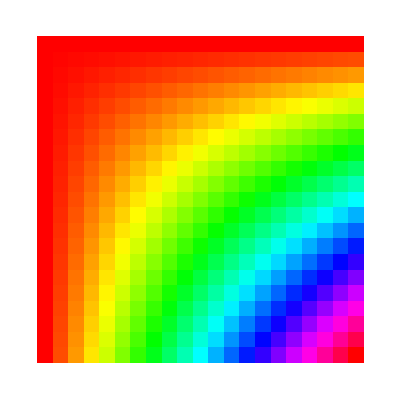

```mathematica
ArrayPlot[Table[Hue[X*Y],{X,0,1,0.05},{Y,0,1,0.05}]]
```

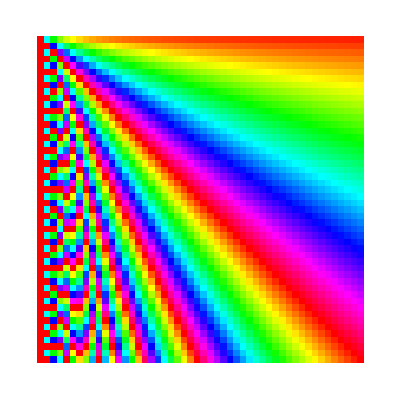

```mathematica
ArrayPlot[Table[Hue[X/Y],{X,1,50,1},{Y,1,50,1}]]
```

```mathematica
ArrayPlot[Table[StringLength[RomanNumeral[x*y]],{x,100},{y,100}]]
```

-Graphics-